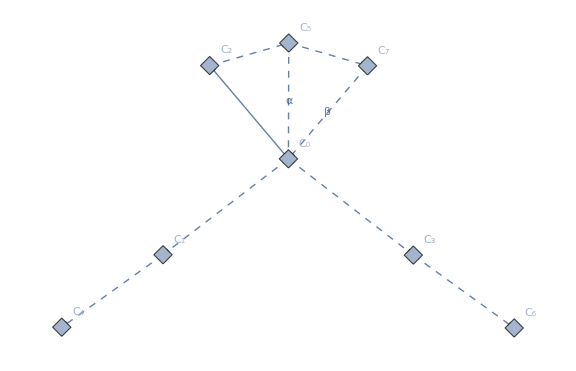

```mathematica
Graph[{Subscript[C, 0]->Subscript[C, 1],Subscript[C, 0]->Subscript[C, 2],Subscript[C, 0]->Subscript[C, 3],Subscript[C, 2]->Subscript[C, 5],Subscript[C, 3]->Subscript[C, 6],Subscript[C, 1]->Subscript[C, 4],Labeled[Subscript[C, 5]->Subscript[C, 0],"α"],Subscript[C, 5]->Subscript[C, 7],Labeled[Subscript[C, 7]->Subscript[C, 0],"β"]},VertexShapeFunction->"Diamond",VertexSize->Medium, VertexLabels->"Name",EdgeStyle->{Subscript[C, 0]->Subscript[C, 3]->Dashed,Subscript[C, 0]->Subscript[C, 1]->Dashed, Subscript[C, 3]->Subscript[C, 6]->Dashed,Subscript[C, 1]->Subscript[C, 4]->Dashed,Subscript[C, 2]->Subscript[C, 5]->Dashed,Subscript[C, 5]->Subscript[C, 0]->Dashed,Subscript[C, 5]->Subscript[C, 0]->Dashed,Subscript[C, 5]->Subscript[C, 7]->Dashed,Subscript[C, 7]->Subscript[C, 0]->Dashed,Subscript[C, 7]->Subscript[C, 0]->Dashed},EdgeShapeFunction->"CarvedArcArrow"]
```

```mathematica
"If one firm chooses OS, the OS FIRM payoff is:"
P -(Subscript[C, 0]-Subscript[C, 2]-Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5]))
"NON-OS FIRM payoff is:"
P -(Subscript[C, 0]-Subscript[α, 0] Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5])-Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1]))

"If both firms choose OS, their payoff is:"
P -(Subscript[C, 0]-Subscript[C, 2]-Subscript[C, 5] Subscript[π, 2](Subscript[C, 2],Subscript[C, 5]))

"If both firms choose patents, one firms payoff is:" 
P -(Subscript[C, 0]-Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1]))
"And the others is:"
P -(Subscript[C, 0]-Subscript[C, 3] π(Subscript[C, 0],Subscript[C, 3]))

"Nash is OS for firm 1 iff"
P -(Subscript[C, 0]-Subscript[C, 2]-Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5]))>P -(Subscript[C, 0]-Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1]))
Subscript[C, 2]+Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5])>Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1])
"and"
P -(Subscript[C, 0]-Subscript[C, 2]-Subscript[C, 5] Subscript[π, 2](Subscript[C, 2],Subscript[C, 5]))>P -(Subscript[C, 0]-Subscript[α, 0] Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5])-Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1]))
Subscript[C, 2]+Subscript[C, 5] Subscript[π, 2](Subscript[C, 2],Subscript[C, 5])>Subscript[α, 0] Subscript[C, 5] Subscript[π, 1](Subscript[C, 2],Subscript[C, 5])+Subscript[C, 1] π(Subscript[C, 0],Subscript[C, 1])
```